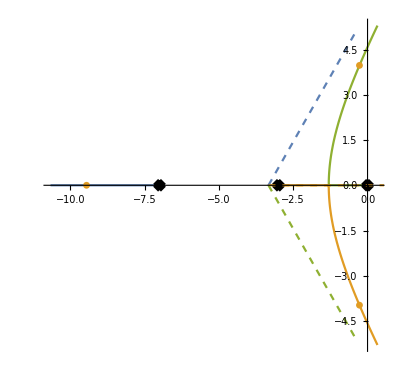

```mathematica
Module[{tfm,p,z,m,σ,asymptotes},
tfm=k/(s(s+3)(s+7))//N;
{p,z}=Flatten/@{TransferFunctionPoles[tfm],TransferFunctionZeros[tfm]};
m=Table[
Tan[((2 j-1) π)/(Length[p]-Length[z])],
{j,1,Length[p]-Length[z]}
];
σ=Chop[(Total[p]-Total[z])/(Length[p]-Length[z])];
asymptotes=m/.{ComplexInfinity->x==σ,m_?NumericQ:>y==m (x-σ)};
Show[
RootLocusPlot[tfm,{k,0,300}],
ContourPlot[Evaluate[asymptotes],
{x,σ,2},{y,-5,5},
ContourStyle->Dashed]
]
]
```